```mathematica
SetDirectory["/Users/dluntzma/Desktop"];
counts1 = Import["2014_double_slit_bulb_counts.csv"];
counts1;
```

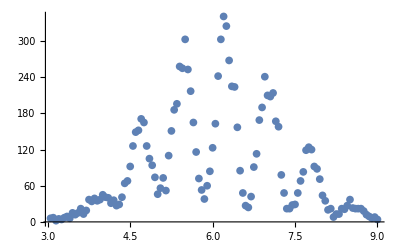

```mathematica
ListPlot[counts1]
```

```mathematica
θ = (x - x0)/R;
α = π * a * Sin[θ]/λ;
β = π * d * Sin[θ]/λ; 

Subscript[i, 2] = i0 * (Sinc[α])^2 * Cos[β]^2;
```

```mathematica
x0= 6.2;
a = 0.085;
d = 0.343;
R = 500;
λ = .000546;
(*i0= 350;*)
```

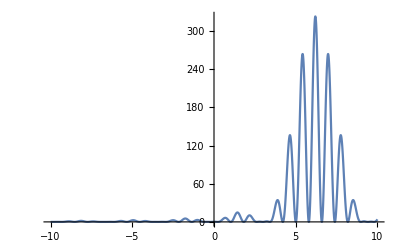

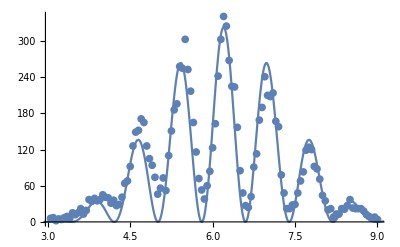

```mathematica
fit1 = NonlinearModelFit[counts1,Subscript[i, 2],{i0}, x];
plot1 = Plot[fit1[x], {x, -10, 10},PlotRange->All]
Show[ListPlot[counts1], plot1]
```